# Whitehead Field Dynamics

## Computational notes

Alexander Kolpakov  ·  September 2026

This notebook accompanies whitehead-field-dynamics-computational-notes.tex. It contains the exact calculations used in that note, together with drawings of the graph-of-graphs models, an interactive view of the cubic multigraph represented by each state, and an exact 71-state diffusion calculation. Proofs remain in the full LaTeX manuscript.

## Start here

Keep this file in the repository root and choose Evaluation > Evaluate Notebook. The first cell loads the local GogFieldDynamics package; no global installation is needed. SetReplace is optional.

Load the companion package

```mathematica
repo=Quiet[Check[NotebookDirectory[],$Failed]];If[!StringQ[repo]||!DirectoryQ[FileNameJoin[{repo,"Wolfram","GogFieldDynamics"}]],repo=Directory[]];PacletDirectoryLoad[FileNameJoin[{repo,"Wolfram","GogFieldDynamics"}]];Needs["GogFieldDynamics`"];Association["GogFieldDynamicsVersion"->PacletObject["GogFieldDynamics"]["Version"],"PackageLoaded"->NameQ["GogFieldDynamics`GogAvailableSizes"]]
```

<|GogFieldDynamicsVersion→0.2.0,PackageLoaded→True|>

## What is being computed

A cubic multigraph is a graph in which every vertex has degree three; loops count twice toward the degree, and parallel edges are allowed. A graph type is an isomorphism class obtained after vertex labels are forgotten. The graph of graphs (GoG) has one vertex for each connected graph type and joins two types when one Whitehead move relates them. Such a move selects a carrier edge, meaning a specific edge in a chosen representative, collapses it, and chooses one of the two other pairings of the four exposed half-edges. A field f in R^N travels with the graph; on a carrier with endpoints i and j, those values are replaced by their common mean.

(f_i,f_j)⟶((f_i+f_j)/2,(f_i+f_j)/2)

Three computational objects must be kept separate.

The carrier field uses the concrete selected edge. After an unlabelled move, a settlement permutation is the relabelling that identifies the result with the stored representative of its graph type; the same permutation is applied to the field coordinates.

Rule A keeps every local outcome slot after labels are forgotten. A cubic graph has 3N/2 edges and two resolutions per edge, hence 3N slots. Different slots leading to the same type retain their multiplicity. A slot returning to the current type is a holding event.

Rule B gives one of the 3N equally weighted slots to each different adjacent graph type and assigns every unused slot to staying put. Its jump chain, called BJump in the code, is the conditional chain given that the graph type changes; removing the holds changes path probabilities and elapsed time.

The local package contains every graph type, every one-move connection, and the exact transition counts for N=2,4,6,8. The N=8 model already has 71 states; larger data sets can be generated separately.

## The graph of graphs

A GoG vertex represents an entire graph type, not one vertex of the underlying cubic multigraph. The small N=4 atlas makes this distinction visible: its five GoG vertices are shown together with the five cubic multigraphs they represent.

N=4 graph of graphs

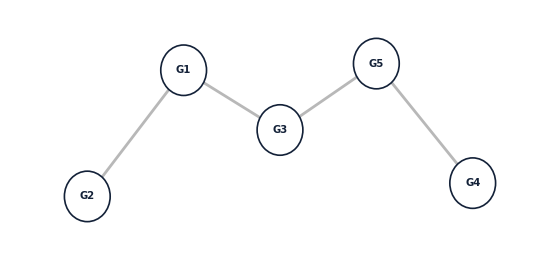
One-move connections between graph types
-Graphics-
The vertices G1, G2, ... represent these cubic multigraphs:
G1
-Graphics- | G2
-Graphics- | G3
-Graphics-
G4
-Graphics- | G5
-Graphics- |

```mathematica
classAtlas=GogClassAtlas[4]
```

The upper diagram shows the one-move connections among G1 through G5. The drawings below it show the cubic multigraph represented by each of those five vertices.

The next output is live and opens on the 71-vertex N=8 model. Choose N=2, 4, 6, or 8, then click any GoG vertex. Hovering gives its G-number; the panel on the right redraws the cubic multigraph represented there.

Inspect a graph type

```mathematica
classExplorer=GogClassExplorer["InitialSize"->8]
```

The selected GoG vertex is orange; its underlying cubic multigraph appears on the right. Labels are suppressed on the 71-state view to keep the graph legible, but every vertex remains clickable.

## The local averaging calculation

For a non-loop pair {i,j}, the averaging matrix is the orthogonal projection onto the hyperplane f_i=f_j.

A_ij=I_N-1/2(e_i-e_j)(e_i-e_j)^T

It is symmetric, idempotent, and fixes the all-ones vector. The two-coordinate energy calculation can be checked without constructing the whole matrix.

Energy lost by averaging one pair

```mathematica
Clear[x,y];FullSimplify[x^2+y^2-2 ((x+y)/2)^2,Assumptions->{x,y}∈Reals]
```

1/2 (x-y)^2

Write the mean as f-bar and the centered energy as V(f). Pair averaging preserves the mean and has an exact one-step loss.

f̄=1/N∑_(k=1)^N f_k
V(f)=∑_(k=1)^N (f_k-f̄)^2
V(A_ij f)=V(f)-(f_i-f_j)^2/2

The averaging matrix

```mathematica
pairAverage[n_,{i_,j_}]:=ReplacePart[IdentityMatrix[n],{{i,i}->1/2,{i,j}->1/2,{j,i}->1/2,{j,j}->1/2}];a=pairAverage[4,{1,3}];Association["Symmetric"->SymmetricMatrixQ[a],"Idempotent"->a.a===a,"Preserves constant fields"->a.ConstantArray[1,4]===ConstantArray[1,4]]
```

<|Symmetric→True,Idempotent→True,Preserves constant fields→True|>

A settlement is a permutation matrix. It preserves sums and Euclidean norms, so it cannot change this one-step variance identity. It can change which persistent pair of field coordinates is averaged later. A list of unlabelled graph types therefore does not contain enough information to reconstruct the later field values.

## Bundled models

For each bundled size, the table records the number of graph types, the number of GoG edges, and the number of Rule A outcomes.

Available small models

```mathematica
modelRows=Table[With[{m=GogSmallModel[n]},{n,m["NodeCount"],m["EdgeCount"],m["RuleASlotCount"]}],{n,GogAvailableSizes[]}];Grid[Prepend[modelRows,{"N","Graph types","GoG edges","Rule A outcomes"}],Frame->All,Alignment->Right]
```

N | Graph types | GoG edges | Rule A outcomes
2 | 2 | 1 | 12
4 | 5 | 4 | 60
6 | 17 | 25 | 306
8 | 71 | 179 | 1704

The class counts 2, 5, 17, and 71 agree with the corresponding terms of OEIS A005967. Multiplying each class count by the 3N possible Rule A outcomes gives the totals below.

c_2·6=12
c_4·12=60
c_6·18=306
c_8·24=1704

The next cell checks that every bundled table is complete, that the node and outcome counts agree, and that every transition row sums to one. It also checks Rule-B symmetry and verifies that a uniform starting distribution remains uniform after one step.

Check the bundled models

```mathematica
r=GogValidateSmallModels[];Association["All bundled models valid"->r["Valid"],"Checks by N"->AssociationMap[r["Models",#1]["Valid"]&,GogAvailableSizes[]]]
```

<|All bundled models valid→True,Checks by N→<|2→True,4→True,6→True,8→True|>|>

## An exact five-state example

At N=4 there are five unlabelled graph types, shown above. Rule A counts every local move outcome, including repeated outcomes that lead to the same graph type.

Rule A move counts

```mathematica
countsA=GogTransitionCounts[4,"A"];{{countsA}, {"Row sums: "Total/@countsA}}
```

(4 | 4 | 4 | 0 | 0
6 | 6 | 0 | 0 | 0
2 | 0 | 8 | 0 | 2
0 | 0 | 0 | 6 | 6
0 | 0 | 4 | 2 | 6)
Row sums: {12,12,12,12,12}

Every row sums to 3N=12. Dividing the count matrix by 12 gives the exact Rule-A transition matrix. It is not symmetric.

P_A=C_A/(3N)

A stationary distribution is a probability row vector pi satisfying pi P = pi. The left 1-eigenspace of P_A gives it exactly.

Stationary distribution for Rule A

```mathematica
pA=GogTransitionMatrix[4,"A"];piA=First[NullSpace[Transpose[pA]-IdentityMatrix[Length[pA]]]];stationaryA=piA/Total[piA];Grid[Prepend[MapIndexed[{"G"<>ToString[First[#2]],#1}&,stationaryA],{"Graph type","Stationary probability"}],Frame->All,Alignment->Right]
```

Graph type | Stationary probability
G1 | 1/5
G2 | 2/15
G3 | 2/5
G4 | 1/15
G5 | 1/5

The distribution is nonuniform because graph types with different numbers of labelled realizations receive different weights. Treating Rule A as uniform on graph types would change the process.

Rule B assigns weight 1/(3N) to each adjacent graph type and puts the unused probability on the diagonal. Its support graph keeps one edge whenever a nonself move is possible and discards all multiplicities; L_supp below is the Laplacian of that simple graph.

P_B(g,h)=1/(3N),g∼h,g≠h
P_B(g,g)=1-(deg(g))/(3N)
I-P_B=L_supp/(3N)

Rule B transition matrix

```mathematica
pB=GogTransitionMatrix[4,"B"];pB
```

(5/6 | 1/12 | 1/12 | 0 | 0
1/12 | 11/12 | 0 | 0 | 0
1/12 | 0 | 5/6 | 0 | 1/12
0 | 0 | 0 | 11/12 | 1/12
0 | 0 | 1/12 | 1/12 | 5/6)

The defining symmetry and stationarity checks can be made directly. For this symmetric transition matrix, the spectral gap means one minus its second-largest eigenvalue.

Symmetry and stationarity

```mathematica
u=ConstantArray[1/5,5];Association["Symmetric matrix"->SymmetricMatrixQ[pB],"Uniform distribution after one step"->u.pB]
```

<|Symmetric matrix→True,Uniform distribution after one step→{1/5,1/5,1/5,1/5,1/5}|>

Rule B eigenvalues and spectral gap

```mathematica
eigenvaluesB=Sort[Eigenvalues[pB],Greater];Association["Eigenvalues of Rule B"->eigenvaluesB,"Spectral gap"->FullSimplify[1-eigenvaluesB⟦2⟧]]
```

<|Eigenvalues of Rule B→{1,1/24 (21+√5),1/24 (19+√5),1/24 (21-√5),1/24 (19-√5)},Spectral gap→1/24 (3-√5)|>

1-λ_2(P_B)=(3-√5)/24

A holding step leaves the graph type unchanged but still consumes one step. Already at N=2, Rule B and its jump chain allow the same changes to other types, yet assign different path probabilities and have different spectra.

Rule B versus its jump chain

```mathematica
{{"Rule B"}, {GogTransitionMatrix[2,"B"]}, {"Jump chain obtained after removing holds"}, {GogTransitionMatrix[2,"BJump"]}}
```

Rule B
(5/6 | 1/6
1/6 | 5/6)
Jump chain obtained after removing holds
(0 | 1
1 | 0)

## Exact diffusion and a sampled path

Here diffusion means the evolution of a probability distribution over graph types: p_t = p_0 P^t. We first start at G1 in the five-state N=4 model and apply Rule A four times so that every exact probability can be inspected directly.

p_t=e_G1^T P^t
p_(t+1)=p_t P,∑_(g∈𝒢_4) p_t(g)=1

Rule A after four steps

```mathematica
p4A=GogDiffusionState[4,"A",1,4];Grid[Prepend[MapIndexed[{"G"<>ToString[First[#2]],#1,N[#1,5]}&,p4A],{"Graph type","Exact probability","Decimal"}],Frame->All,Alignment->Right]
```

Graph type | Exact probability | Decimal
G1 | 185/648 | 0.28549
G2 | 49/216 | 0.22685
G3 | 59/162 | 0.3642
G4 | 1/54 | 0.018519
G5 | 17/162 | 0.10494

All five classes are reachable by time four, but the mass is far from the stationary vector. From the same starting point, Rule B retains much more probability at G1 because it more often stays in place.

Rule B after four steps

```mathematica
p4B=GogDiffusionState[4,"B",1,4];Grid[Prepend[MapIndexed[{"G"<>ToString[First[#2]],#1,N[#1,5]}&,p4B],{"Graph type","Exact probability","Decimal"}],Frame->All,Alignment->Right]
```

Graph type | Exact probability | Decimal
G1 | 5623/10368 | 0.54234
G2 | 1181/5184 | 0.22782
G3 | 4121/20736 | 0.19874
G4 | 41/20736 | 0.0019772
G5 | 151/5184 | 0.029128

These distributions live on graph types. Transporting a scalar field under Rule B additionally requires a rule for choosing the actual carrier edge to average. The next calculation moves to the complete N=8 GoG: blue encodes the exact 71-state distribution at t=12, while orange traces a separate 48-step sample.

N=8 diffusion and a 48-step sample

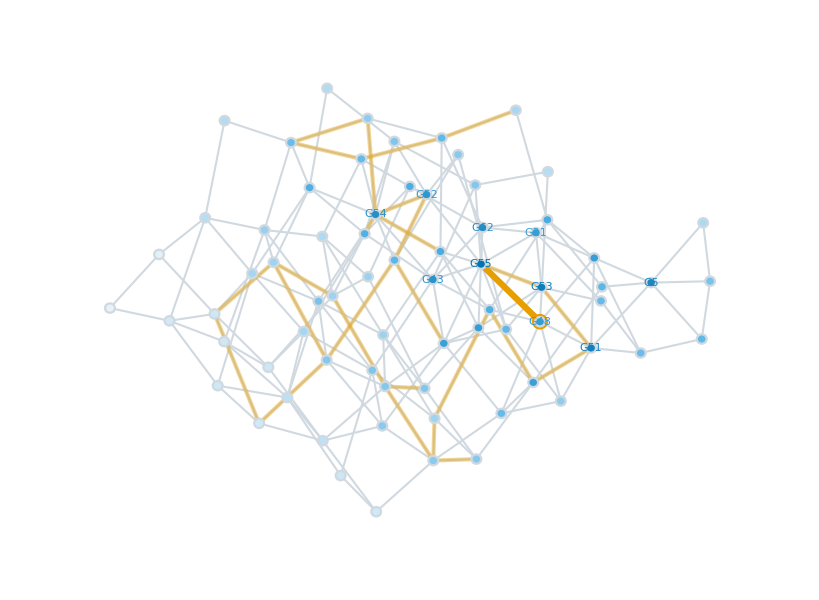
Rule A after 12 steps from G1 on the N = 8 graph of graphs
-Graphics-
Ten largest probabilities at t = 12
Graph | Probability
G55 | 0.065
G53 | 0.055
G51 | 0.052
G5 | 0.047
G62 | 0.041
G54 | 0.040
G43 | 0.038
G52 | 0.034
G48 | 0.031
G21 | 0.030
Total shown: 0.433
Sample path: 48 steps, seed 273
t = 0–8   G1  →  G28  →  G24  →  G29  →  G29  →  G9  →  G54  →  G9  →  G54
t = 8–16   G54  →  G54  →  G34  →  G54  →  G25  →  G54  →  G52  →  G20  →  G27
t = 16–24   G27  →  G20  →  G61  →  G61  →  G71  →  G69  →  G63  →  G63  →  G61
t = 24–32   G61  →  G61  →  G63  →  G36  →  G37  →  G66  →  G37  →  G49  →  G64
t = 32–40   G64  →  G64  →  G64  →  G64  →  G64  →  G49  →  G49  →  G49  →  G45
t = 40–48   G45  →  G26  →  G26  →  G26  →  G58  →  G51  →  G53  →  G55  →  G48
Blue encodes the exact rational distribution at t = 12. Orange marks the separate sampled path.

```mathematica
diffusionPicture=GogDiffusionSnapshot[8,"A",1,12,273,"PathSteps"->48]
```

Path data used in the picture

```mathematica
samplePath=GogRandomTrajectory[8,"A",1,48,273];pathRows=MapIndexed[{First[#2]-1,"G"<>ToString[#1]}&,samplePath];pathBlocks=Table[PadRight[Take[pathRows,{start,Min[start+12,Length[pathRows]]}],13,{{"",""}}],{start,{1,14,27,40}}];{{Association["Transitions"->Length[samplePath]-1,"Distinct graph types visited"->Length[DeleteDuplicates[samplePath]],"Holding steps"->Count[Partition[samplePath,2,1],{x_,x_}]]}, {Grid[Prepend[MapThread[Join,pathBlocks],Flatten[ConstantArray[{"t","state"},4]]],Frame->All,Alignment->Right]}}
```

<|Transitions→48,Distinct graph types visited→27,Holding steps→13|>
t | state | t | state | t | state | t | state
0 | G1 | 13 | G54 | 26 | G63 | 39 | G49
1 | G28 | 14 | G52 | 27 | G36 | 40 | G45
2 | G24 | 15 | G20 | 28 | G37 | 41 | G26
3 | G29 | 16 | G27 | 29 | G66 | 42 | G26
4 | G29 | 17 | G20 | 30 | G37 | 43 | G26
5 | G9 | 18 | G61 | 31 | G49 | 44 | G58
6 | G54 | 19 | G61 | 32 | G64 | 45 | G51
7 | G9 | 20 | G71 | 33 | G64 | 46 | G53
8 | G54 | 21 | G69 | 34 | G64 | 47 | G55
9 | G54 | 22 | G63 | 35 | G64 | 48 | G48
10 | G34 | 23 | G63 | 36 | G64 |  | 
11 | G54 | 24 | G61 | 37 | G49 |  | 
12 | G25 | 25 | G61 | 38 | G49 |  |

The path visits 27 different graph types. Its 13 repeated consecutive labels are holding steps, and the fixed seed makes the sample reproducible.

## Finite-time consensus

Consensus means that every field coordinate equals the arithmetic mean of the initial field. Finite-time consensus means this happens after a finite product of pair-averaging matrices, equivalently that the product equals J_N. A perfect matching is a set of disjoint pairs covering all N coordinates. For such a matching, M denotes the product of its commuting pair averages; successive products act from right to left.

J_N=1/N 1_N(1_N)^T
J_N f=f̄ 1_N
M_(13|24)=A_13 A_24
M_(13|24)M_(12|34)=J_4
M_(15|26|37|48)M_(13|24|57|68)M_(12|34|56|78)=J_8

Verify the consensus products

```mathematica
matching[n_,edges_]:=Dot@@(pairAverage[n,#1]&)/@edges;k4Product=matching[4,{{1,3},{2,4}}].matching[4,{{1,2},{3,4}}];q3Product=matching[8,{{1,5},{2,6},{3,7},{4,8}}].matching[8,{{1,3},{2,4},{5,7},{6,8}}].matching[8,{{1,2},{3,4},{5,6},{7,8}}];Association["K4 reaches exact consensus"->k4Product===ConstantArray[1/4,{4,4}],"Q3 reaches exact consensus"->q3Product===ConstantArray[1/8,{8,8}]]
```

<|K4 reaches exact consensus→True,Q3 reaches exact consensus→True|>

For example, the K4 product is returned exactly as the consensus matrix.

The K4 product

```mathematica
k4Product
```

(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4)

Every initial field therefore reaches its exact mean after the stated schedule. This exceptional finite-time consensus should not be extrapolated to arbitrary N. Every entry of a finite product of pair averages has denominator a power of two, whereas the mean of (0,0,1) requires a factor 1/3.

## References

Laura Grave de Peralta and Alexander Kolpakov, Expansion properties of Whitehead moves on cubic graphs, Comptes Rendus Mathematique 362 (2024), 1825-1836. https://doi.org/10.5802/crmath.691

Michael Li, Increasingly Many Bounded Eigenvalues of the Graph of Whitehead Moves, arXiv:2405.14592. https://arxiv.org/abs/2405.14592

Proofs are in whitehead-field-dynamics.tex.